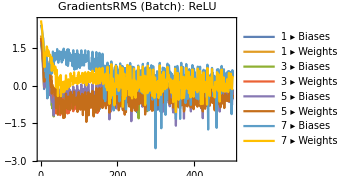
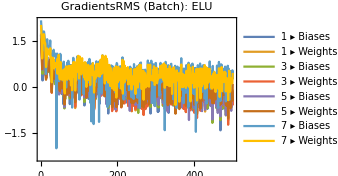
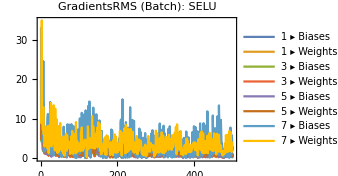
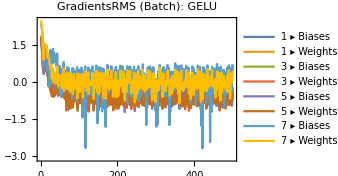
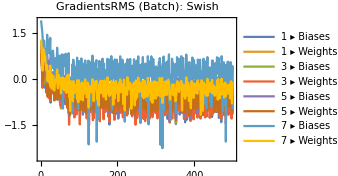
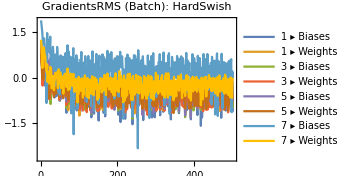
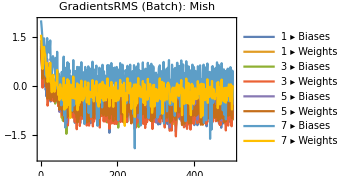
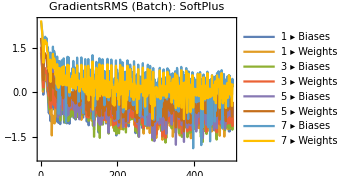

```mathematica
(* The code aims to generate synthetic training data using a Gaussian-modulated exponential function with added noise and systematically evaluate the performance of various activation functions in a neural network. It achieves this by defining a neural network architecture with three hidden layers, each followed by one of the specified activation functions,and training the network on the generated data. During training, the GradientsRMS property is monitored to ensure proper training dynamics,and results are recorded for each activation function. This approach provides insights into how different activation functions impact the training process and performance of the neural network: *)

(* Generate the training data using a Gaussian-modulated exponential function with added noise: *)
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

(* Training data with added noise: *)
trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

(* Set up array for activation functions: *)
activationFunctions={
"ReLU","ELU","SELU",
"GELU","Swish","HardSwish",
"Mish","SoftPlus","HardTanh",
"HardSigmoid","Sigmoid",Tanh
};

(* Loop through each activation function, train a neural network, and record the results: *)
results=Table[
Module[
{net,trainedNet},
(* Define a simple neural network structure: *)
net=NetChain[
{
(* First hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Second hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Third hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Output layer with linear activation function: *)
LinearLayer[1]
}
];
(* Train the network on training data: *)
trainedNet=NetTrain[
net,
trainingData,
(* Monitor training progress using GradientsRMS property: *)
<|
"Property"->"GradientsRMS",
"Form"->"EvolutionPlot",
"PlotOptions"->{PlotLabel->Style[Row[{"GradientsRMS (Batch): ",functions}],12,Bold],ImageSize->250},
"Interval"->"Batch"
|>,
(* Specify mean squared loss as the training objective: *)
LossFunction->MeanSquaredLossLayer[],
(* Set the batch size for training: *)
BatchSize->64,
(* Learning rate for "ADAM": *)
LearningRate->0.01,
(* Use "ADAM" as the optimization method: *)
Method->"ADAM",
(* Maximum number of training iterations: *)
MaxTrainingRounds->50
]
],
(* Iterate over the grid of activation functions: *)
{functions,activationFunctions}
]
```

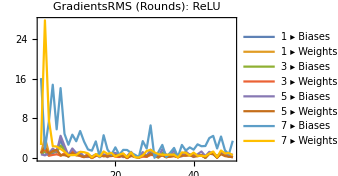
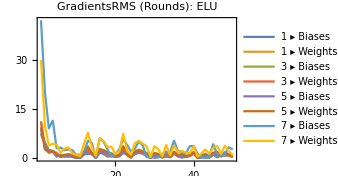
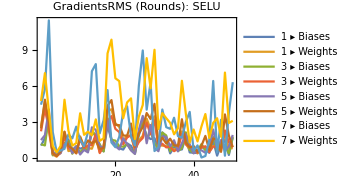
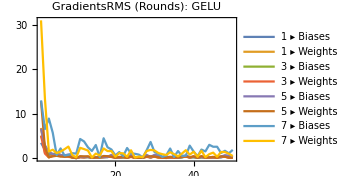
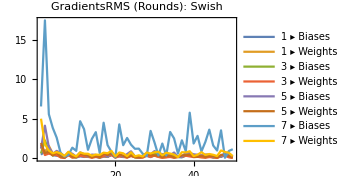
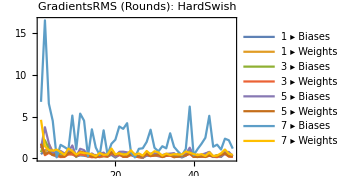
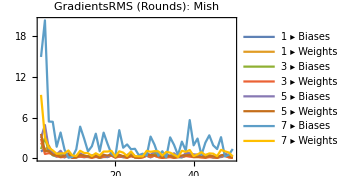
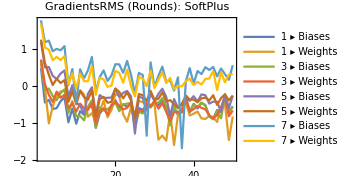

```mathematica
(* The above and the following codes are largely similar, both aiming to generate synthetic training data, train a neural network using various activation functions,and monitor the training process. However, they differ in how they monitor the training progress: the above code monitors the GradientsRMS property at the "Batch" interval,providing a more granular view of the gradient changes, while the following code monitors it at the "Rounds" interval, offering a broader view: *)

(* Generate the training data using a Gaussian-modulated exponential function with added noise: *)
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

(* Training data with added noise: *)
trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

(* Set up array for activation functions: *)
activationFunctions={
"ReLU","ELU","SELU",
"GELU","Swish","HardSwish",
"Mish","SoftPlus","HardTanh",
"HardSigmoid","Sigmoid",Tanh
} ;

(* Loop through each activation function, train a neural network, and record the results: *)
results=Table[
Module[
{net,trainedNet},

(* Define a simple neural network structure: *)
net=NetChain[
{
(* First hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Second hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Third hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Output layer with linear activation function: *)
LinearLayer[1]  
}
];

(* Train the network on training data: *)
trainedNet=NetTrain[
net,
trainingData,
(* Monitor training progress using GradientsRMS (Rounds) property: *)
<|
"Property"->"GradientsRMS",
"Form"->"EvolutionPlot",
"PlotOptions"->{ PlotLabel->Style[Row[{"GradientsRMS (Rounds): ",functions}],12,Bold],ImageSize->250},
"Interval"->"Rounds"
|>,
(* Specify mean squared loss as the training objective: *)
LossFunction->MeanSquaredLossLayer[],
(* Set the batch size for training: *)
BatchSize->64,
(* Learning rate for "ADAM": *)
LearningRate->0.01,
(* Use "ADAM" as the optimization method: *)
Method->"ADAM",
(* Maximum number of training iterations: *)
MaxTrainingRounds->50
]
],
(* Iterate over the grid of activation functions: *)
{functions,activationFunctions}
]
```

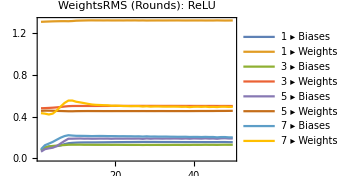
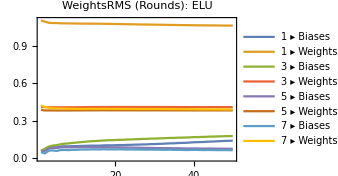
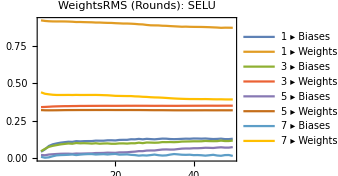
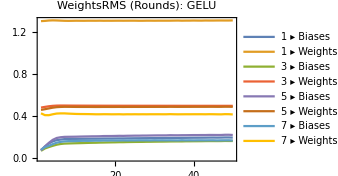
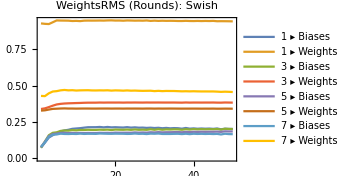
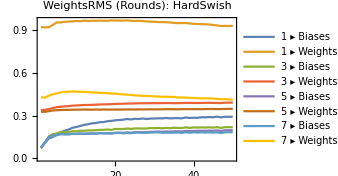
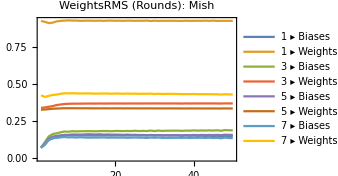
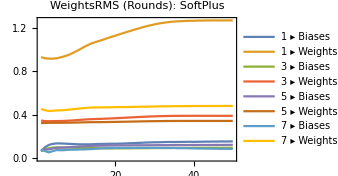

```mathematica
(* In this case, training progress is monitored using the WeightsRMS property at the "Rounds" interval. By recording and analyzing the results for each activation function, the code provides insights into their impact on the training dynamics and performance of the neural network: *)

(* Generate the training data using a Gaussian-modulated exponential function with added noise: *)
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

(* Training data with added noise: *)
trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

(* Set up arrays for hyperparameter tuning: Activation Functions  *)
activationFunctions={
"ReLU","ELU","SELU",
"GELU","Swish","HardSwish",
"Mish","SoftPlus","HardTanh",
"HardSigmoid","Sigmoid",Tanh
} ;

(* Loop through each activation function, train a neural network, and record the results: *)
results=Table[
Module[
{net,trainedNet},

(* Define a simple neural network structure: *)
net=NetChain[
{
(* First hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Second hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Third hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Output layer with linear activation function: *)
LinearLayer[1]  
}
];

(* Train the network on training data: *)
trainedNet=NetTrain[
net,
trainingData,
(* Monitor training progress using WeightsRMS (Rounds) property: *)
<|
"Property"->"WeightsRMS",
"Form"->"EvolutionPlot",
"PlotOptions"->{ PlotLabel->Style[Row[{"WeightsRMS (Rounds): ",functions}],12,Bold],
ImageSize->250},
"Interval"->"Rounds"
|>,
(* Specify mean squared loss as the training objective: *)
LossFunction->MeanSquaredLossLayer[],
(* Set the batch size for training: *)
BatchSize->64,
(* Learning rate for "ADAM": *)
LearningRate->0.01,
(* Use "ADAM" as the optimization method: *)
Method->"ADAM",
(* Maximum number of training iterations: *)
MaxTrainingRounds->50
]
],
(* Iterate over the grid of activation functions: *)
{functions,activationFunctions}
]
```

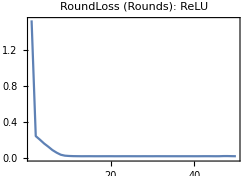
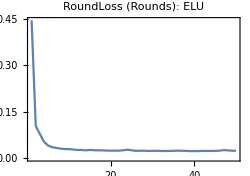
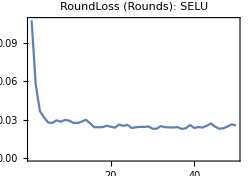
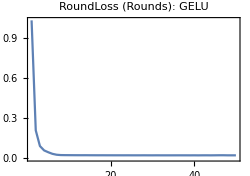
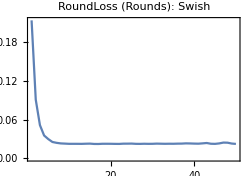
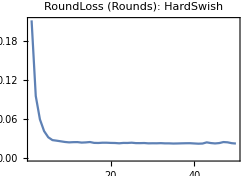
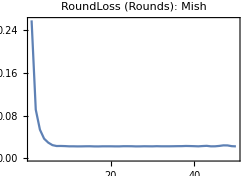
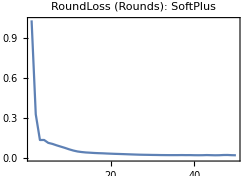

```mathematica
(* In this case, training progress is monitored using the RoundLoss property at the "Rounds" interval. By recording and analyzing the results for each activation function,the code provides insights into their impact on the training dynamics and performance of the neural network,aiding in the selection of suitable activation functions for future designs: *)

(* Generate the training data using a Gaussian-modulated exponential function with added noise: *)
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

(* Training data with added noise: *)
trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

(* Set up arrays for hyperparameter tuning: Activation Functions  *)
activationFunctions={
"ReLU","ELU","SELU",
"GELU","Swish","HardSwish",
"Mish","SoftPlus","HardTanh",
"HardSigmoid","Sigmoid",Tanh} ;

(* Loop through each activation function, train a neural network, and record the results: *)
results=Table[
Module[
{net,trainedNet},

(* Define a simple neural network structure: *)
net=NetChain[
{
(* First hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Second hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Third hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Output layer with linear activation function: *)
LinearLayer[1]  
}
];

(* Train the network on training data: *)
trainedNet=NetTrain[
net,
trainingData,
(* Monitor training progress using RoundLoss property: *)
<|
"Property"->"RoundLoss",
"Form"->"EvolutionPlot",
"PlotOptions"->{PlotLabel->Style[Row[{"RoundLoss (Rounds): ",functions}],12,Bold],
ImageSize->250},
"Interval"->"Rounds"
|>,
(* Specify mean squared loss as the training objective: *)
LossFunction->MeanSquaredLossLayer[],
(* Set the batch size for training: *)
BatchSize->64,
(* Learning rate for "ADAM": *)
LearningRate->0.01,
(* Use "ADAM" as the optimization method: *)
Method->"ADAM",
(* Maximum number of training iterations: *)
MaxTrainingRounds->50
]
],
(* Iterate over the grid of activation functions: *)
{functions,activationFunctions}
]
```

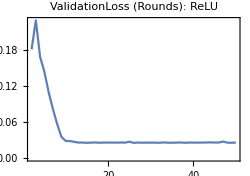
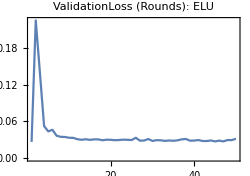
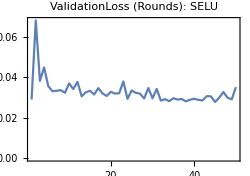
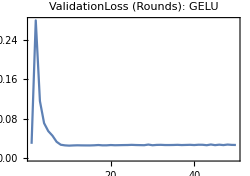
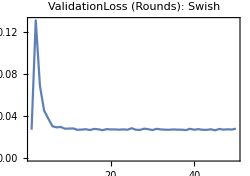
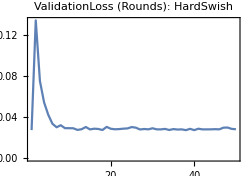
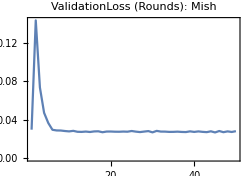
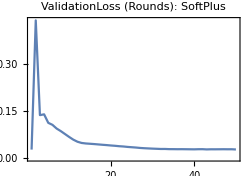

```mathematica
(* In this case, training progress is monitored using the ValidationLoss property at the "Rounds" interval. By recording and analyzing the results for each activation function,the code provides insights into their impact on the training dynamics and performance of the neural network,aiding in the selection of suitable activation functions for future designs: *)

(* Generate the training data using a Gaussian-modulated exponential function with added noise: *)
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

(* Training data with added noise: *)
trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

(* Validation data with added noise: *)
validationData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

(* Set up arrays for hyperparameter tuning: Activation Functions  *)
activationFunctions={
"ReLU","ELU","SELU",
"GELU","Swish","HardSwish",
"Mish","SoftPlus","HardTanh",
"HardSigmoid","Sigmoid",Tanh
} ;

(* Loop through each activation function, train a neural network, and record the results: *)
results=Table[
Module[
{net,trainedNet},

(* Define a simple neural network structure: *)
net=NetChain[
{
(* First hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Second hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Third hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Output layer with linear activation function: *)
LinearLayer[1]  
}
];

(* Train the network on training data and validate it: *)
trainedNet=NetTrain[
net,
trainingData,
(* Monitor training progress using ValidationLoss (Rounds) property: *)
<|
"Property"->"ValidationLoss",
"Form"->"EvolutionPlot",
"PlotOptions"->{PlotLabel->Style[Row[{"ValidationLoss (Rounds): ",functions}],12,Bold],
ImageSize->250},
"Interval"->"Rounds"
|>,
ValidationSet->validationData,
(* Specify mean squared loss as the training objective: *)
LossFunction->MeanSquaredLossLayer[],
(* Set the batch size for training: *)
BatchSize->64,
(* Learning rate for "ADAM": *)
LearningRate->0.01,
(* Use "ADAM" as the optimization method: *)
Method->"ADAM",
(* Maximum number of training iterations: *)
MaxTrainingRounds->50
]
],
(* Iterate over the grid of activation functions: *)
{functions,activationFunctions}
]
```

{{ReLU,0.0218124},{ELU,0.0206307},{SELU,0.0213209},{GELU,0.020704},{Swish,0.0206826},{HardSwish,0.0208644},{Mish,0.0202925},{SoftPlus,0.0201096},{HardTanh,0.0213772},{HardSigmoid,0.020397},{Sigmoid,0.0208766},{Tanh,0.0205486}}

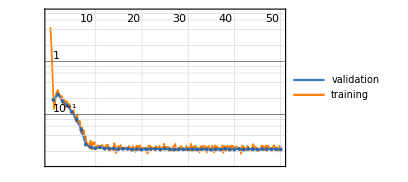
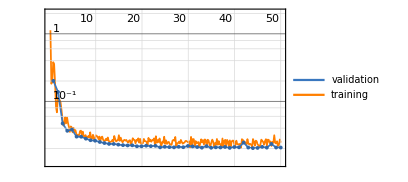
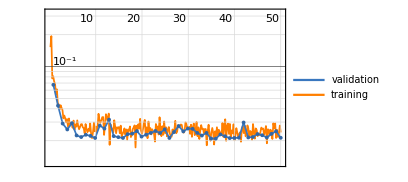
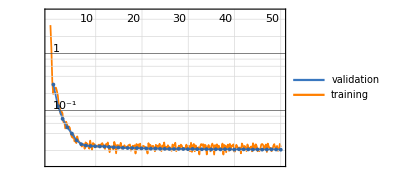
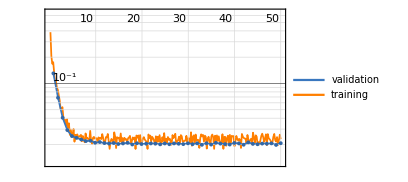
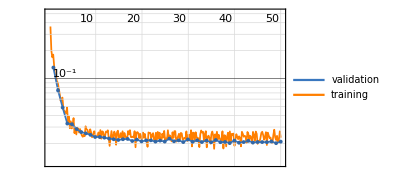
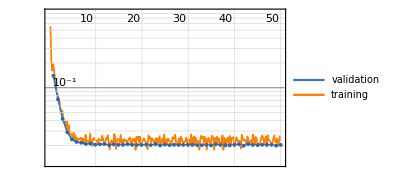
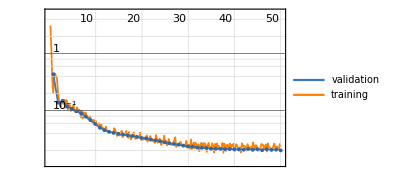
{ | rounds
loss | -Graphics-ReLU, | rounds
loss | -Graphics-ELU, | rounds
loss | -Graphics-SELU, | rounds
loss | -Graphics-GELU, | rounds
loss | -Graphics-Swish, | rounds
loss | -Graphics-HardSwish, | rounds
loss | -Graphics-Mish, | rounds
loss | -Graphics-SoftPlus, | rounds
loss | -Graphics-HardTanh, | rounds
loss | -Graphics-HardSigmoid, | rounds
loss | -Graphics-Sigmoid, | rounds
loss | -Graphics-Tanh}

```mathematica
(* The code aims to generate synthetic training data using a Gaussian-modulated exponential function with added noise,and systematically evaluate various activation functions in a neural network by training and validating the network with each function. It defines a neural network architecture with three hidden layers and an output layer,each hidden layer using one of the specified activation functions. The network is trained on the generated data using the ADAM optimization method with mean squared loss as the objective, and its performance is validated using a separate validation data set. The training progress is monitored using mean square error (MSE) measurements,and results, including validation MSE and loss plots,are recorded for each activation function. This process provides insights into the impact of different activation functions on the training dynamics and performance of neural networks,aiding in the selection of appropriate activation functions for future designs: *)

(* Generate the training data using a Gaussian-modulated exponential function with added noise: *)
dataFunction[x_]:=Exp[-x^2];
noiseLevel=0.15;

(* Training data with added noise: *)
trainingData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.01}
];

(* Validation data with added noise: *)
validationData=Table[
x->dataFunction[x]+RandomVariate[NormalDistribution[0,noiseLevel]],
{x,-3,3,0.1}
];

(* Set up array for activation functions  *)
activationFunctions={
"ReLU","ELU","SELU",
"GELU","Swish","HardSwish",
"Mish","SoftPlus","HardTanh",
"HardSigmoid","Sigmoid",Tanh} ;

(* Loop through each activation function, train a neural network, and record the results: *)
results=Table[
Module[
{net,trainedNet,validationMSE},

(* Define a simple neural network structure: *)
net=NetChain[
{
(* First hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Second hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Third hidden layer with specified activation function: *)
LinearLayer[10],ElementwiseLayer[functions],
(* Output layer with linear activation function: *)
LinearLayer[1]  
}
];

(* Train the network on training data and validate it: *)
trainedNet=NetTrain[
net,
trainingData,
All,
ValidationSet->validationData,
TrainingProgressMeasurements->{"MeanSquare"},
(* Specify mean squared loss as the training objective: *)
LossFunction->MeanSquaredLossLayer[],
(* Set the batch size for training: *)
BatchSize->64,
(* Learning rate for "ADAM": *)
LearningRate->0.01,
(* Use "ADAM" as the optimization method: *)
Method->"ADAM",
(* Maximum number of training iterations: *)
MaxTrainingRounds->50
];

(* Calculate MSE on validation data for model evaluation: *)

(* Extract validation MSE from training results: *)
validationMSE=Values[trainedNet["ValidationMeasurements"]][[2]];
(* Get the loss plot from training results: *)
lossplot=trainedNet["LossPlot"];
(* Return validation MSE,trained network,and loss plot: *)
{validationMSE,trainedNet,lossplot}
],
(* Iterate over the grid of activation functions: *)
{functions,activationFunctions}
];

(* Create a table of activation functions and their corresponding validation MSE: *)
Table[
{activationFunctions[[i]],results[[i]][[1]]},
{i,1,12}]

(* Create overlays of loss plots and activation functions: *)
Table[
Overlay[{results[[i]][[3]],activationFunctions[[i]]},Alignment->{0.9,0.4}],
{i,1,12}
]
```